## OBC strained graphene

```mathematica
nuc=8;t0=2.8;
width=3*nuc;height=2*width;inFrac=0.35;
L=Max[{width,height}];
a=1;L1=L+1;L2=L+1;
a1=a/2{3,√3,0};
a2=a/2{3,-√3,0};
b1={a,0,0};
uc = {0*b1,b1};

latt=Flatten[Table[{n1*a1+n2*a2+uc[[i]],i},{n1,L1},{n2,L2},{i,Length[uc]}],2];
meanPosition=Mean[latt[[All,1]]];
latt[[All,1]]=(#-meanPosition)&/@latt[[All,1]];
lattRegion=DeleteCases[latt,_?(Not[(-width/2<#[[1,1]]<width/2)&&(-height/2<#[[1,2]]<(height-2)/2)]&)];

rB=Max[lattRegion[[All,1]][[All,1]]];lB=Min[lattRegion[[All,1]][[All,1]]];
tB=Max[lattRegion[[All,1]][[All,2]]];bB=Min[lattRegion[[All,1]][[All,2]]];
lrPos=Flatten[Position[lattRegion[[All,1]][[All,1]],n_ /; n==#]]&/@{rB,lB};
tbPos=Flatten[Position[lattRegion[[All,1]][[All,2]],n_ /; n==#]]&/@{tB,bB};
bPos=Join[lrPos,tbPos];

cL=IntegerPart[Length[tbPos[[2]]]/2];
inR = IntegerPart[cL*inFrac];
inPos = tbPos[[2,cL-inR+1;;-(cL-inR+1)]];
bPos=Complement[#,inPos]&/@bPos;

lattCols={Darker[Red],Lighter[Red]};
boundaryCols={Darker[Green],Lighter[Green]};
injectionCols={Darker[Blue],Lighter[Blue]};

latt=lattRegion;
lattBR=latt[[#]]&/@Flatten[bPos];
lattIN=latt[[#]]&/@Flatten[inPos];
dimH = Length[latt];

Clear[lattRegions]
Evaluate[Table[lattRegions[i],{i,Length[uc]}]]=Evaluate[Table[DeleteCases[latt,_?(Not[#[[2]]==i]&)],{i,Length[uc]}]];
lattPlot=Graphics3D[Table[{lattCols[[#[[2]]]],Sphere[#[[1]],0.3]}&/@lattRegions[i],{i,{1,2}}]];
boundaryPlot=Graphics3D[{boundaryCols[[#[[2]]]],Sphere[#[[1]],0.3]}&/@lattBR];
injectionPlot=Graphics3D[{injectionCols[[#[[2]]]],Sphere[#[[1]],0.3]}&/@lattIN];
nodesPlot=Show[lattPlot,boundaryPlot,injectionPlot,ViewPoint->Top]
```

-Graphics3D-

```mathematica
nnPlot=Graphics3D[{{Black,CapForm["Butt"],Tube[{latt[[#[[1]],1]],latt[[#[[2]],1]]},.1]}&/@neighbors[[2]]},ViewPoint->Top];
Show[nodesPlot,nnPlot,ViewPoint->Top,Axes->True]
```

-Graphics3D-

```mathematica
dist[n1_,n2_]:=Norm[n2-n1];
dists=Outer[dist,latt[[All,1]],latt[[All,1]],1];
ddists=DeleteDuplicates[Chop[dists//Flatten]]//Sort;
neighbors=Position[dists,#,3]&/@ddists[[;;2]];
```

```mathematica
strainField[n_,σn_]:=N[1/(√(2π σn^2)) Exp[(-Norm[n]^2)/(2 σn^2) ]]
```

```mathematica
deformedLatt={Chop[#[[1]]+20{0,0,strainField[#[[1]],2]}],#[[2]]}&/@latt;
```

```mathematica
nnPlot=Graphics3D[{{Black,CapForm["Butt"],Tube[{deformedLatt[[#[[1]],1]],deformedLatt[[#[[2]],1]]},.1]}&/@neighbors[[2]]},ViewPoint->Top];
Show[nodesPlot,nnPlot,ViewPoint->Top,Axes->True]
```

-Graphics3D-

```mathematica
(* custom eigensystem *)
Clear[orderedEigensystem]
orderedEigensystem[M_,f_:Re]:=Module[{eigsys, order},
eigsys = Eigensystem[M];
order = Ordering[f[eigsys[[1]]]];
{eigsys[[1,order]],eigsys[[2,order]]ᵀ}
];
```

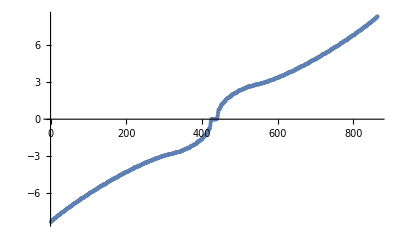

True

```mathematica
(* now the Hamiltonian matrix is simply given by the nearest neighbor connections *)
H =Normal[SparseArray[#-> t0&/@neighbors[[2]]]];
{energies,wavefunctions}=orderedEigensystem[H]//Sort;
imEnergies=Im[energies];
energies=Re[energies];
ListPlot[energies]
max=Max[energies];
min=Min[energies];
DeleteDuplicates[Chop[wavefunctions†.H.wavefunctions-DiagonalMatrix[energies]]//Flatten]=={0}
(*Histogram[energies,{min,max,(max-min)/54},"Probability",PlotRange->{{-1.5,1.5},Automatic}]*)
```

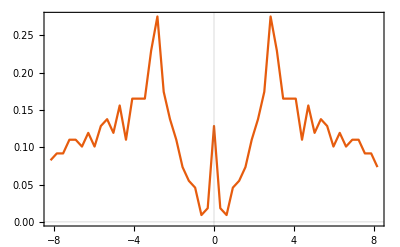

```mathematica
{bene,bvals}=HistogramList[energies,{min,max,(max-min)/53},Probability];
ListPlot[{MovingAverage[bene,2],bvals*2*π}ᵀ,Joined->True,PlotTheme->"Scientific"]
```

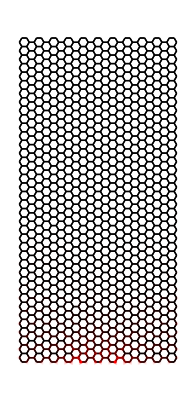

```mathematica
η=1/t;
Σ=SparseArray[{#,#}->- ⅈ η&/@(bPos//Flatten)];

ene=0.2;
Kp={0,(+4π)/(3 √3),0};
Km={0,(-4π)/(3 √3),0};
Cp=0.0;
Cm=1.0;
kx=0;
ky=ene;
ϕ=If[ky==0,π/2,ArcTan[kx/ky]];
σ=Sign[ene];

Clear[χ]
χ[1][r_,k_,σ_,ϕ_]:=Cm*ⅇ^(ⅈ(k+Km).r)+Cp*ⅇ^(ⅈ(k+Kp).r)
χ[2][r_,k_,σ_,ϕ_]:=σ Cm ⅇ^(ⅈ(k+Km).r + ⅈ ϕ)-σ Cp ⅇ^(ⅈ(k+Kp).r - ⅈ ϕ)
inTuples=Tuples[{inPos,inPos}];
ΣinP=0*H;
(ΣinP[[Sequence@@#]]=χ[latt[[#[[1]],2]]][latt[[#[[1]],1]],{kx,ky,0},+1,ϕ]* χ[latt[[#[[2]],2]]][latt[[#[[2]],1]],{kx,ky,0},+1,ϕ])&/@inTuples;
G=Inverse[N[H-ene*IdentityMatrix[Dimensions[H]]-Σ]];
GP = G.ΣinP.G†;
GP=GP/Max[Abs[Diagonal[GP,1]]];
nP = Re[Diagonal[(GP+GP†)]];
ppP = Abs[nP]/If[(w=Max[Abs[nP]])>1*^-8,w,1];

bg=Graphics[{{{Black,CapForm["Butt"],Line[{latt[[All,1]][[#[[1]],1;;2]],latt[[All,1]][[#[[2]],1;;2]]}]}&/@neighbors[[2]]}}];
Show[bg,Graphics[{{Directive[Opacity[(#[[1]])^(1)],Red],Disk[#[[2,1;;2]],0.3]}&/@({ppP,latt[[All,1]]}ᵀ),{{Directive[Red,Opacity[Abs[Im[GP[[Sequence@@#]]]]]],CapForm["Butt"],Arrow[{latt[[All,1]][[#[[1]],1;;2]],latt[[All,1]][[#[[2]],1;;2]]}]}&/@neighbors[[2]]}}]]
```

```mathematica
RAM Expensive!!!
```

```mathematica
wavefunctions†.wavefunctions;
ppExact=Diagonal[{#}ᵀ.{#}*]&/@(wavefunctionsᵀ);
gsExact=({#}ᵀ.{#}*)&/@(wavefunctionsᵀ);
gsExact=gsExact/Max[gsExact];
ppExact = ppExact/Max[ppExact];
bg=Graphics[{{{Black,CapForm["Butt"],Line[{latt[[All,1]][[#[[1]],1;;2]],latt[[All,1]][[#[[2]],1;;2]]}]}&/@neighbors[[2]]}}];

<<MaTeX`
Manipulate[Show[bg,Graphics[{{Directive[Opacity[#[[1]]],Red],Disk[#[[2,1;;2]],0.3]}&/@({ppExact[[i]],latt[[All,1]]}ᵀ),{{Directive[Blue,Opacity[Im[gsExact[[i,Sequence@@#]]]]],CapForm["Butt"],Arrow[{latt[[All,1]][[#[[1]],1;;2]],latt[[All,1]][[#[[2]],1;;2]]}]}&/@neighbors[[2]]}}],PlotLabel->MaTeX[StringForm["|\\psi_{E=``t}|^2",DecimalForm[energies[[i]],{4,4}]]]],{{i,IntegerPart[Length[ppExact]/2]},1,Length[ppExact],1}]
```

```mathematica
η=1*^2;
Gs={};
ees=Range[-3,3,0.1];
ees = energies;
Σ=SparseArray[{#,#}->- ⅈ η&/@(bPos//Flatten)];
Monitor[
Do[
AppendTo[Gs,Inverse[N[H-ee*IdentityMatrix[Dimensions[H]]-Σ]]];
,{ee,ees}],ee]
Clear[BlockAverage]
BlockAverage[xs_,r_]:=Table[Mean[xs[[i;;i+r]]],{i,1,Length[xs]-r,r}]
As=Plus@@Re[Diagonal[-ⅈ*(#-#†)]]&/@Gs;
As/=Plus@@As;
rBlock=Max[IntegerPart[Length[ees]/50],1];
mAs=BlockAverage[As,rBlock];
mees=BlockAverage[ees,rBlock];
mAs/=Plus@@mAs;
ListPlot[{mees,mAs 2π}ᵀ,Joined->True,PlotRange->Full,PlotLabel->"Spectral function (block average)"]
ListPlot[{ees,As 2π}ᵀ,Joined->True,PlotRange->Full,PlotLabel->"Spectral function"]
ns = Re[Diagonal[(#+#†)]]&/@Gs;
pp = Abs[#]/If[(w=Max[Abs[#]])>1*^-8,w,1]&/@ns;
bg=Graphics[{{{Black,CapForm["Butt"],Line[{latt[[All,1]][[#[[1]],1;;2]],latt[[All,1]][[#[[2]],1;;2]]}]}&/@neighbors[[2]]}}];(*Manipulate[Show[bg,Graphics[{{Directive[Opacity[#[[1]]],Red],Disk[#[[2,1;;2]],0.3]}&/@({pp[[i]],latt[[All,1]]}ᵀ),{{Directive[Blue,Opacity[Abs[η*Im[Gs[[i,Sequence@@#]]]]]],CapForm["Butt"],Arrow[{latt[[All,1]][[#[[1]],1;;2]],η*Im[Gs[[i,Sequence@@#]]](latt[[All,1]][[#[[2]],1;;2]]-latt[[All,1]][[#[[1]],1;;2]])+latt[[All,1]][[#[[1]],1;;2]]}]}&/@neighbors[[2]]}}],PlotLabel->MaTeX[StringForm["|\\psi_{E=``t}|^2",DecimalForm[ees[[i]],{4,4}]]]],{{i,IntegerPart[Length[pp]/2]},1,Length[pp],1}]*)
```